## Non-linear wobbling

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[I_,A1_,A2_,A3_]:=If[A1>=1||A2>=1||A3>=1||(A1<A3&&A2>A3)||(A1>A3&&A2<A3),2.1*10^9,A3*I(I+1)+2I √((A1-A3)(A2-A3))];
```

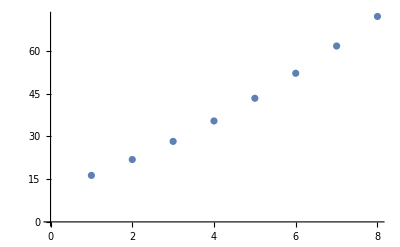

```mathematica
ListPlot[Table[f[x,0.2,0.3,0.1],{x,11,25,2}]]
```

```mathematica
wobexp={0.433,0.416,0.366,0.322,0.276,0.216,0.151,0.181};
spins={11,13,15,17,19,21,23,25};
makedata[data_]:=Table[{spins[[i]],data[[i]]},{i,1,Length[data]}];
dataexp=makedata[wobexp];
```

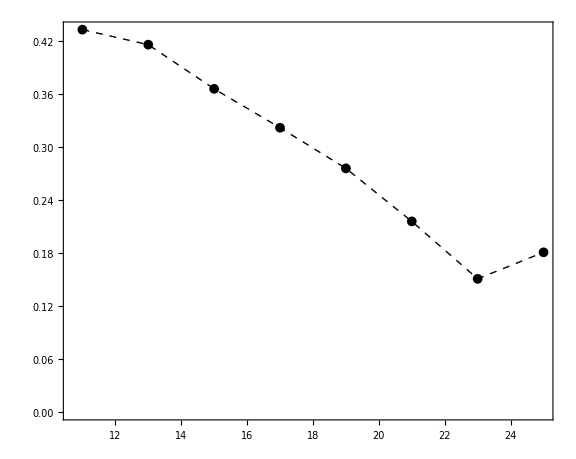

```mathematica
ListPlot[dataexp,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{Thick,Black,Dashed},ImageSize->Large,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],Frame->True,Axes->False]
```

```mathematica
nlm=NonlinearModelFit[dataexp,f[x,a,b,c],{a,b,c},x]
```

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

FittedModel[2.1×10^9]

```mathematica
nlm["ParameterTable"]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1. | Indeterminate | Indeterminate | Indeterminate
b | 1. | Indeterminate | Indeterminate | Indeterminate
c | 1. | Indeterminate | Indeterminate | Indeterminate